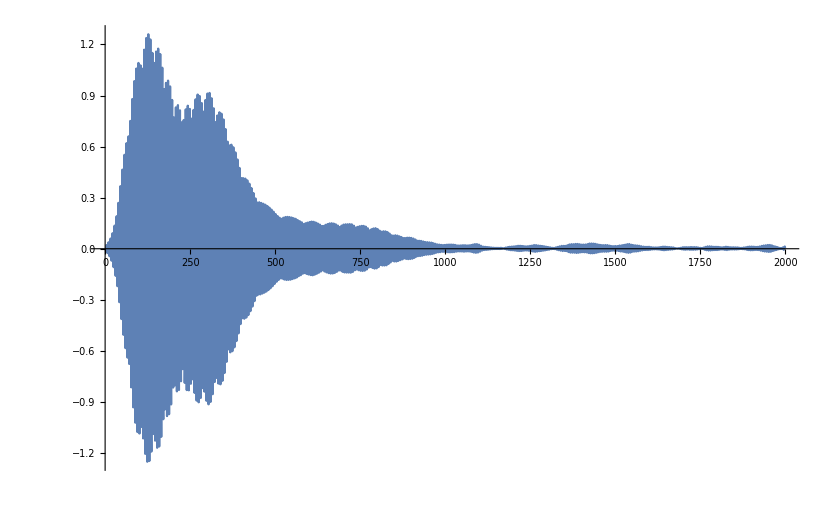

```mathematica
ListPlot[Re[InverseFourier[Table[{(n-1)/(nf-ni+1)/.{ni->2,nf->2000},(((0.0001/(0.0001+(((n-1)/(nf-ni+1))-0.17)^2))+(0.0001/(0.0001+(((n-1)/(nf-ni+1))-(1-0.17))^2)))/.{ni->2,nf->2000})Fourier[data0[[Range[ni/.{ni->2,nf->2000},nf/.{ni->2,nf->2000}],3]]][[n]]},{n,(nf-ni+1)/.{ni->2,nf->2000}}][[All,2]]]][[Range[1,1999]]],PlotRange->All,Joined->True,PlotMarkers->None]
```

```mathematica
h:=1/2(k11 Jx^3/2 Sqrt[Jy]+k12 Sqrt[Jx] Jy^3/2)(Cos[ϕx-ϕy+η n 2π])+3/8(p Jx^2+r Jy^2+2 q Jx Jy)-3/4f2 Jx Jy (Cos[2ϕx-2ϕy+2η n 2π])+k1 Cos[ϕx+2 π s(νx+νy+η)/2-wr s]Sqrt[Jx]+k2 Cos[ϕy+2 π s(νx+νy-η)/2-wr s]Sqrt[Jy]
ϕxstr=D[h,Jx];
Jxstr=-D[h,ϕx];
ϕystr=D[h,Jy];
Jystr=-D[h,ϕy];
Jxstrd=Jxstr/.{Jx->Jx[t],Jy->Jy[t],ϕx->ϕx[t],ϕy->ϕy[t]};
Jystrd=Jystr/.{Jx->Jx[t],Jy->Jy[t],ϕx->ϕx[t],ϕy->ϕy[t]};
ϕxstrd=ϕxstr/.{Jx->Jx[t],Jy->Jy[t],ϕx->ϕx[t],ϕy->ϕy[t]};
ϕystrd=ϕystr/.{Jx->Jx[t],Jy->Jy[t],ϕx->ϕx[t],ϕy->ϕy[t]};
```

```mathematica
inputpr=({Jx'[t]==Jxstrd,Jy'[t]==Jystrd,ϕx'[t]==ϕxstrd,ϕy'[t]==ϕystrd,Jx[0]==Jxv,Jy[0]==Jyv,ϕx[0]==ϕxv,ϕy[0]==ϕyv}/.{f2->f2,k11->k11,k12->k12,p->p,r->r,q->q,η->η,n->t,k1->k1,k2->k2,νx->νx,νy->νy,wr->wr,s->t});
```

```mathematica
inloc=inputpr/.{Jxv->a^2/100,Jyv->b^2/100,ϕxv->ϕa,ϕyv->ϕb,f2->50,k11->0,k12->0,p->0,r->0,q->-0,η->0.001,k1->.0,k2->.0,νx->.17,νy->.17,wr->.1715,n->t};
tablesol=Table[Flatten[NDSolve[inloc,{Jx[t],ϕx[t],Jy[t],ϕy[t]},{t,0,1000}]],{a,.1,.1,.01},{b,.1,.1,.01},{ϕa,0,2π-0.01,2π/10},{ϕb,0,2π-0.01,2π/10}];
```

```mathematica
podsum=Table[(10((a b)/(2 π σx σy)^2(Sqrt[Jx[t]/.(tablesol[[i,j,k,l]])]/.{t->t1})Cos[2π νx0 n+ϕa+(ϕx[t]/.(tablesol[[i,j,k,l]]))/.{t->t1}]Exp[-(a^2+Z1^2)/(2σx^2)]Exp[-(b^2+Z2^2)/(2σy^2)]Exp[(Z1 a Sin[ϕa])/σx^2]Exp[(Z2 b Sin[ϕb])/σy^2])/.{σx->.01,σy->.01,Z1->.1,Z2->.1,νx0->0.1705,n->t1,a->0.1+0.01(i-1),b->0.1+0.01(j-1),ϕa->0+2π(k-1)/10,ϕb->0+2π(l-1)/10}) (2π/10 )(2π/10),{i,1,1},{j,1,1},{k,1,10},{l,1,10}];
```

```mathematica
tablea=Table[{t1,Total[Flatten[podsum]]},{t1,0,1000,1}];
```

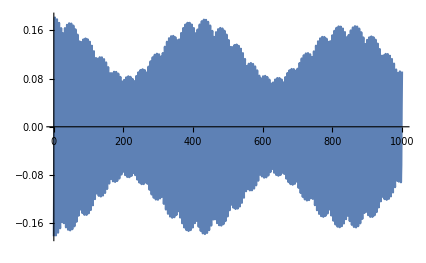

```mathematica
ListPlot[tablea,Joined->True,PlotRange->All]
```

```mathematica
podsumb=Table[(10((a b)/(2 π σx σy)^2(Sqrt[Jy[t]/.(tablesol[[i,j,k,l]])]/.{t->t1})Cos[2π νy0 n+ϕb+(ϕy[t]/.(tablesol[[i,j,k,l]]))/.{t->t1}]Exp[-(a^2+Z1^2)/(2σx^2)]Exp[-(b^2+Z2^2)/(2σy^2)]Exp[(Z1 a Sin[ϕa])/σx^2]Exp[(Z2 b Sin[ϕb])/σy^2])/.{σx->.01,σy->.01,Z1->.1,Z2->.1,νy0->0.1695,n->t1,a->0.1+0.01(i-1),b->0.1+0.01(j-1),ϕa->0+2π(k-1)/10,ϕb->0+2π(l-1)/10})(2π/10 )(2π/10),{i,1,1},{j,1,1},{k,1,10},{l,1,10}];
```

```mathematica
tableb=Table[{t1,Total[Flatten[podsumb]]},{t1,0,1000,1}];
```

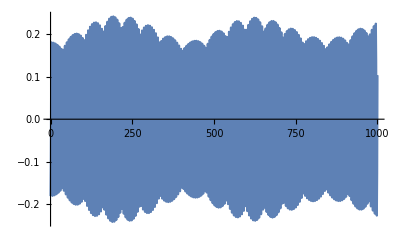

```mathematica
ListPlot[tableb,Joined->True,PlotRange->All]
```

```mathematica
a1=wx Cos[γ];
a1c=wx Cos[γ];
a3=wy Sin[γ] ;
a3c=wy Sin[γ];
b1=-Sin[γ]wx ;
b1c=-Sin[γ]wx ;
b3=wy Cos[γ];
b3c=wy Cos[γ] ;
```

```mathematica
x=a1 tablea[[All,2]]+b1 tableb[[All,2]];
y=a3 tablea[[All,2]]+b3 tableb[[All,2]];
```

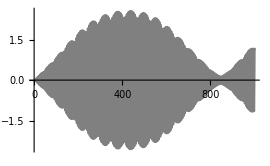

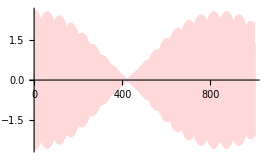

```mathematica
plotx=ListPlot[x[[Range[0,1000]]]/.{wx->10,γ->π/4,wy->10},PlotStyle->Gray,PlotRange->All,Joined->True]
ploty=ListPlot[y/.{wx->10,γ->π/4,wy->10,α->0},PlotStyle->LightRed,PlotRange->All,Joined->True]
```

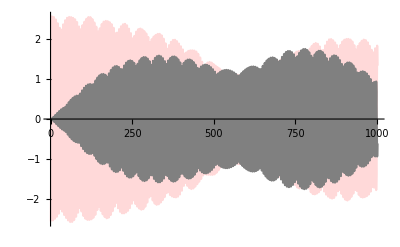

```mathematica
Show[{ploty,plotx}]
```

```mathematica
xwind=Table[(Sin[i π/1000])^2 x[[i]],{i,0,1000}];
ywind=Table[(Sin[i π/1000])^2 y[[i]],{i,0,1000}];
```

```mathematica
listfourierx=Abs[Fourier[xwind/.{wx->10,γ->π/4,wy->10}]];
listfouriery=Abs[Fourier[ywind/.{wx->10,γ->π/4,wy->10,α->0}]];
```

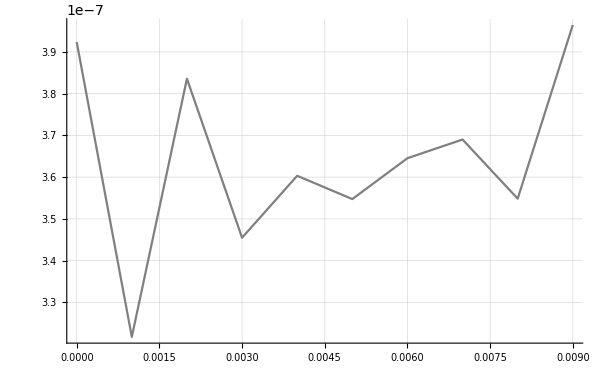

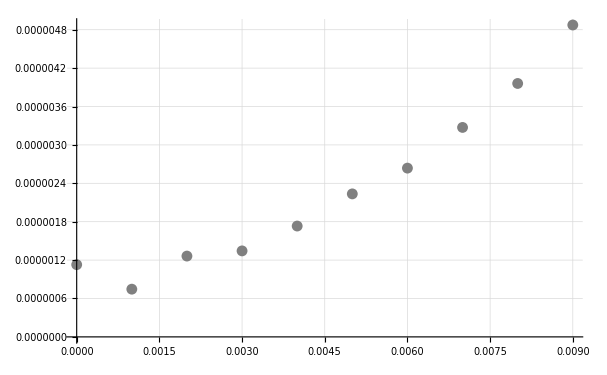

```mathematica
ListPlot[Table[{(n1-1)/(1000),listfourierx[[n1]]},{n1,1,1001}][[Range[0,10]]],PlotStyle->Gray,PlotRange->All,Joined->True,GridLines->Automatic]
ListPlot[Table[{(n1-1)/(1000),listfouriery[[n1]]},{n1,1,1001}][[Range[0,10]]],PlotStyle->Gray,PlotRange->All,Joined->False,GridLines->Automatic]
```

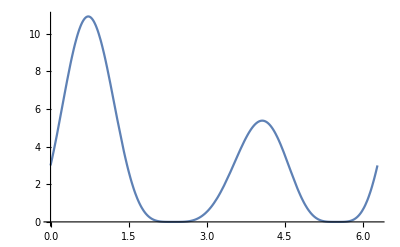

```mathematica
Plot[(2+Cos[x])(1+Sin[2x])^2,{x,0,2π}]
```

```mathematica
inloc=inputpr/.{Jxv->a^2/100,Jyv->b^2/100,ϕxv->ϕa,ϕyv->ϕb,f2->10,k11->0,k12->0,p->0,r->0,q->-0,η->0.001,k1->.0,k2->.0,νx->.17,νy->.17,wr->.1715,n->t};
tablesol=Table[Flatten[NDSolve[inloc,{Jx[t],ϕx[t],Jy[t],ϕy[t]},{t,0,1000}]],{a,.1,.1,.01},{b,.1,.1,.01},{ϕa,0,2π-0.01,2π},{ϕb,0,2π-0.01,2π}];
```

```mathematica
podsum=Table[(((Sqrt[Jx[t]/.(tablesol[[i,j,k,l]])]/.{t->t1})Cos[2π νx0 n 0+ϕa+(ϕx[t]/.(tablesol[[i,j,k,l]]))/.{t->t1}])/.{σx->.01,σy->.01,Z1->.1,Z2->.1,νx0->0.1705,n->t1,a->0.1+0.01(i-1),b->0.1+0.01(j-1),ϕa->0+2π(k-1)/10,ϕb->0+2π(l-1)/10}) ,{i,1,1},{j,1,1},{k,1,1},{l,1,1}];
```

```mathematica
tablea=Table[{t1,Total[Flatten[podsum]]},{t1,0,1000,1}];
```

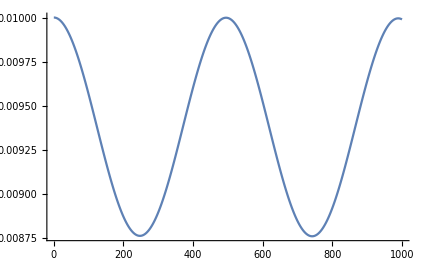

```mathematica
ListPlot[tablea,Joined->True,PlotRange->All]
```

```mathematica
podsumb=Table[(((Sqrt[Jy[t]/.(tablesol[[i,j,k,l]])]/.{t->t1})Cos[2π νy0 n 0+ϕb+(ϕy[t]/.(tablesol[[i,j,k,l]]))/.{t->t1}])/.{σx->.01,σy->.01,Z1->.1,Z2->.1,νy0->0.1695,n->t1,a->0.1+0.01(i-1),b->0.1+0.01(j-1),ϕa->0+2π(k-1)/10,ϕb->0+2π(l-1)/10}),{i,1,1},{j,1,1},{k,1,1},{l,1,1}];
```

```mathematica
tableb=Table[{t1,Total[Flatten[podsumb]]},{t1,0,1000,1}];
```

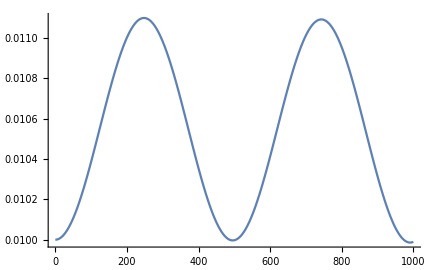

```mathematica
ListPlot[tableb,Joined->True,PlotRange->All]
```

```mathematica
a1=wx Cos[γ];
a1c=wx Cos[γ];
a3=wy Sin[γ] ;
a3c=wy Sin[γ];
b1=-Sin[γ]wx ;
b1c=-Sin[γ]wx ;
b3=wy Cos[γ];
b3c=wy Cos[γ] ;
```

```mathematica
x=a1 tablea[[All,2]]+b1 tableb[[All,2]];
y=a3 tablea[[All,2]]+b3 tableb[[All,2]];
```

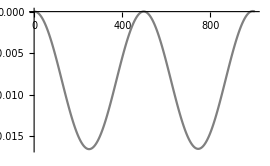

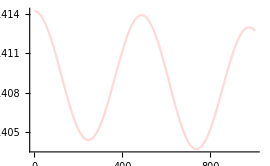

```mathematica
plotx=ListPlot[x[[Range[0,1000]]]/.{wx->10,γ->π/4,wy->10},PlotStyle->Gray,PlotRange->All,Joined->True]
ploty=ListPlot[y/.{wx->10,γ->π/4,wy->10,α->0},PlotStyle->LightRed,PlotRange->All,Joined->True]
```

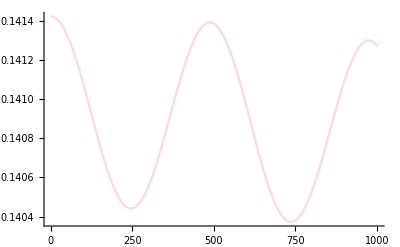

```mathematica
Show[{ploty,plotx}]
```

```mathematica
xwind=Table[(Sin[i π/1000])^2 x[[i]],{i,0,1000}];
ywind=Table[(Sin[i π/1000])^2 y[[i]],{i,0,1000}];
```

```mathematica
listfourierx=Abs[Fourier[xwind/.{wx->10,γ->π/4,wy->10}]];
listfouriery=Abs[Fourier[ywind/.{wx->10,γ->π/4,wy->10,α->0}]];
```

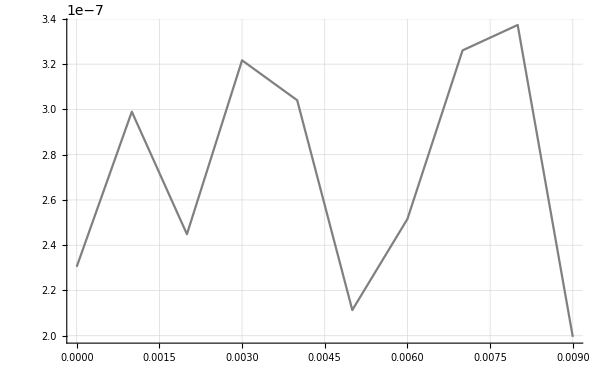

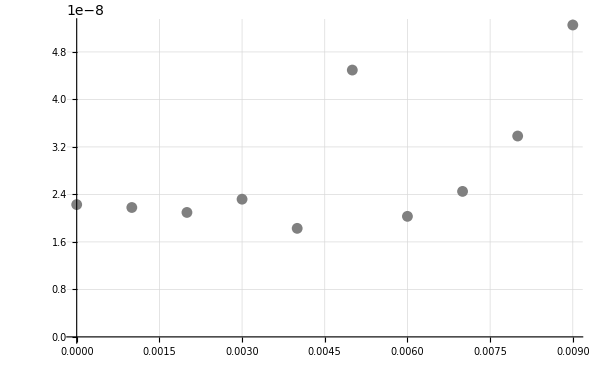

```mathematica
ListPlot[Table[{(n1-1)/(1000),listfourierx[[n1]]},{n1,1,1001}][[Range[0,10]]],PlotStyle->Gray,PlotRange->All,Joined->True,GridLines->Automatic]
ListPlot[Table[{(n1-1)/(1000),listfouriery[[n1]]},{n1,1,1001}][[Range[0,10]]],PlotStyle->Gray,PlotRange->All,Joined->False,GridLines->Automatic]
```

```mathematica
Plot[(2+Cos[x])(1+Sin[2x])^2,{x,0,2π}]
```

-Graphics-

```mathematica
TrigReduce[2+2(Cos[2z])^2+Cos[z](1-(Cos[2z])^2)]
```

1/4 (12+2 Cos[z]-Cos[3 z]+4 Cos[4 z]-Cos[5 z])